0.745443

-0.666569

0.666569

0.745443

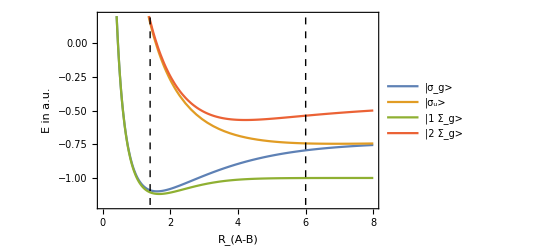

h2-curve.pdf

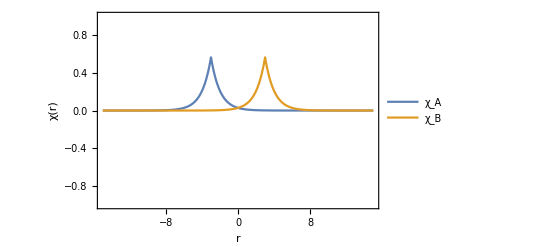

h-aos.pdf

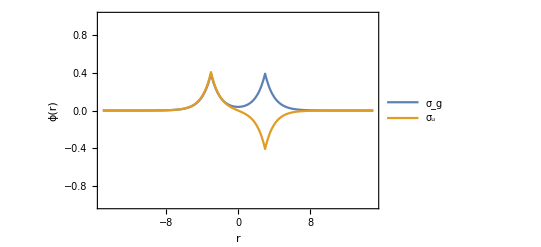

h-mos.pdf

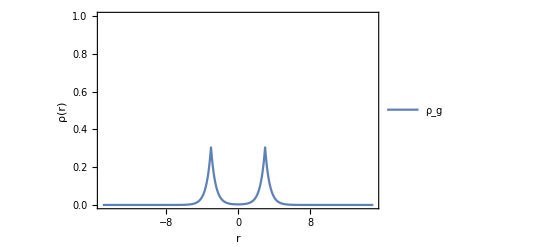

rho1-uncorr-g.pdf

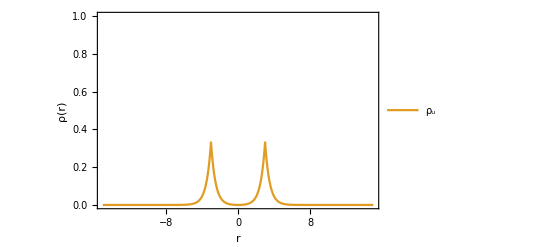

rho1-uncorr-u.pdf

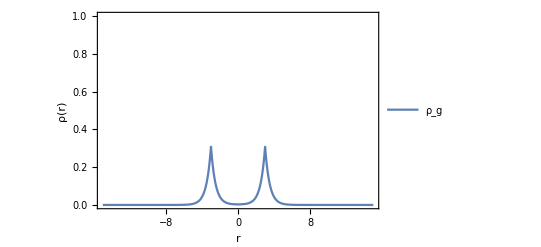

rho1-corr-g.pdf

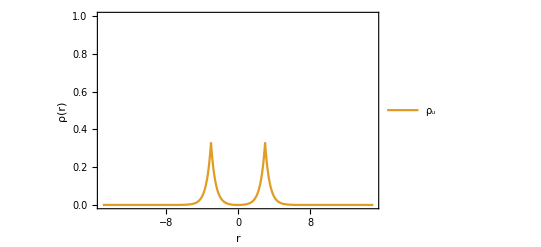

rho1-corr-u.pdf

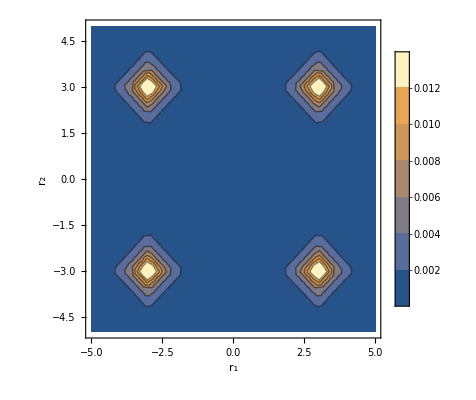

rho2-uncorr-g-cont.pdf

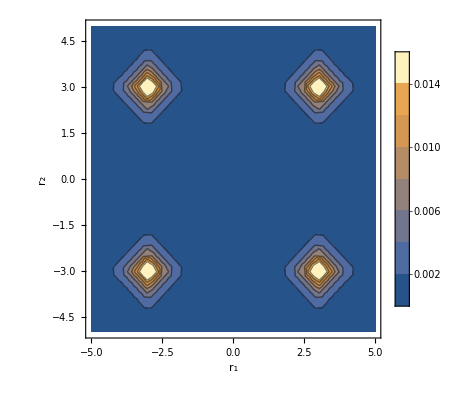

rho2-uncorr-u-cont.pdf

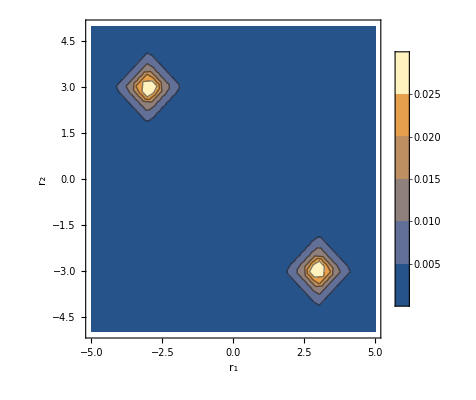

rho2-corr-g-cont.pdf

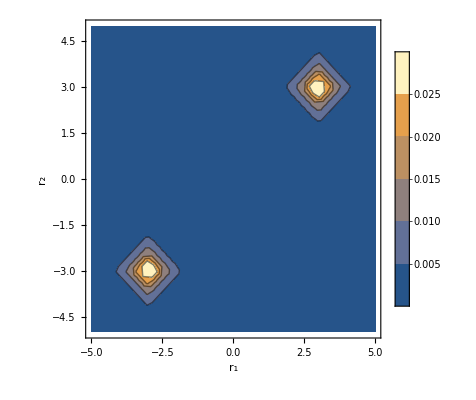

rho2-corr-u-cont.pdf

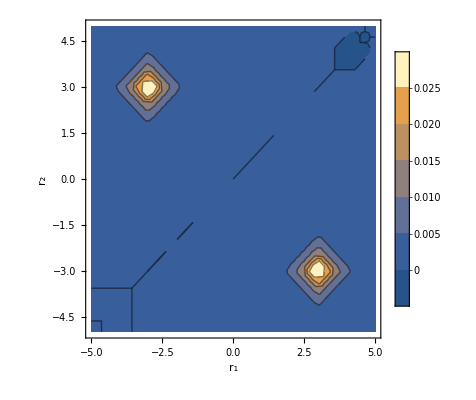

rho2-ferm-para-cont.pdf

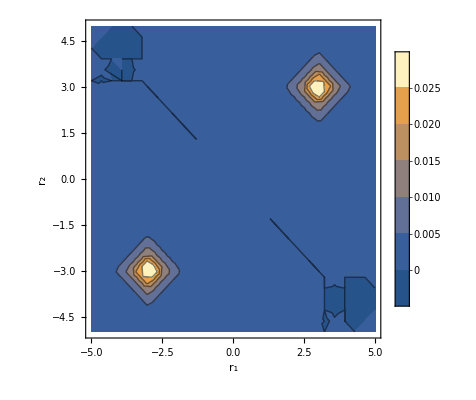

rho2-ferm-anti-cont.pdf

-Graphics3D-

rho2-uncorr-g.pdf

-Graphics3D-

rho2-uncorr-u.pdf

-Graphics3D-

rho2-corr-g.pdf

-Graphics3D-

rho2-corr-u.pdf

-Graphics3D-

rho2-ferm-para.pdf

-Graphics3D-

rho2-ferm-anti.pdf

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->15}];
SetOptions[ContourPlot,BaseStyle->{FontFamily->"Times",FontSize->15}];
SetOptions[Plot3D,BaseStyle->{FontFamily->"Times",FontSize->15}];

(* Parameter *)
zeta=1.0;
r12= 1.4;
 b1=2.0; b2=5.0 
(* b1=5.0; b2=15; *)
rho = zeta*r12;

(* overlap *)
sab[x_]:=(ax=Abs[x];(1.+ax+ax*ax/3.) Exp[-ax]);

(* AO integrals *)
haa[x_]:=(ax=Abs[x]; zeta^2/2-zeta+zeta/ax * (Exp[-2ax] (1+ax)-1));
hab[x_]:=(ax=Abs[x];(zeta^2/2 (1+ax-ax^2/3)-2zeta (1+ax))Exp[-ax]);
gaaaa[x_]:=5zeta/8;
gaabb[x_]:=(ax=Abs[x];zeta(1/ax-Exp[-2 ax](1/ax+11/8+3 ax/4+ax^2/6)));
gaaab[x_]:=(ax=Abs[x];zeta Exp[-ax]/(16 ax)(5+2ax+16ax^2-(5+2ax)Exp[-2ax]));
gabab[x_]:=(ax=Abs[x];zeta Exp[-2 ax]/(120 ax)(75 ax - 138 ax^2 -72ax^3-8ax^4+16(EulerGamma+Log[ax])(9+18ax+15ax^2+6ax^3+ax^4)-32(9-3ax^2+ax^4)Exp[2ax]ExpIntegralEi[-2ax]+16(3-3ax+ax^2)Exp[4ax]ExpIntegralEi[-4ax]));

(* orbitals *)
chia[r_]:=Sqrt[zeta^3/Pi]Exp[-zeta Abs[r+r12/2.]];
chib[r_]:=Sqrt[zeta^3/Pi]Exp[-zeta Abs[r-r12/2.]];
sigg[r_]:=1./Sqrt[2.*(1.+sab[rho])] (chia[r]+chib[r]);
sigu[r_]:=1./Sqrt[2.*(1.-sab[rho])] (chia[r]-chib[r]);
sg2[r_]:=sigg[r]*sigg[r];
su2[r_]:=sigu[r]*sigu[r];

(* MO integrals *)
h11[x_]:=(hab[x]+haa[x])/(1+sab[x])
h22[x_]:=(haa[x]-hab[x])/(1-sab[x])
g1111[x_]:=(gaaaa[x]+4gaaab[x]+gaabb[x]+2gabab[x])/(2(1+sab[x])^2)
g2222[x_]:=(gaaaa[x]-4gaaab[x]+gaabb[x]+2gabab[x])/(2(1-sab[x])^2)
g1212[x_]:=(gaaaa[x]-gaabb[x])/(2(1-sab[x]^2))

(* Energies *)
Esigg[x_]:=2h11[x]+g1111[x]+1/x;
Esigu[x_]:=2h22[x]+g2222[x]+1/x;

(* correlation *)
delta[x_]:=h22[x]-h11[x]+(g2222[x]-g1111[x])/2.;
sigma[x_]:=Sqrt[delta[x]*delta[x]+g1212[x]*g1212[x]];
Ecorg[x_]:=delta[x]-sigma[x];
Ecoru[x_]:=delta[x]+sigma[x];

ccorg[x_]:=-g1212[x]/(delta[x]+sigma[x]);
ccoru[x_]:=-g1212[x]/(delta[x]-sigma[x]);

c1g[x_]:=1./(Sqrt[1+ccorg[x]^2]);
N[c1g[r12]]

c2g[x_]=ccorg[x]/(Sqrt[1+ccorg[x]^2]);
N[c2g[r12]]

c1u[x_]=1./(Sqrt[1+ccoru[x]^2]);
N[c1u[r12]]

c2u[x_]=ccoru[x]/(Sqrt[1+ccoru[x]^2]);
N[c2u[r12]]

(* 1e densities at 1.4 Bohr*)
d1sigg[r_]:=2.sg2[r];
d1sigu[r_]:=2.su2[r];
d1corg[r_]:=c1g[r]^2d1sigg[r]+c2g[r]^2d1sigu[r];
d1coru[r_]:=c1u[r]^2d1sigg[r]+c2u[r]^2d1sigu[r];

(* 2e densities at 1.4 Bohr *)
d2sigg[r1_,r2_]:=1/4. d1sigg[r1]d1sigg[r2];
d2sigu[r1_,r2_]:=1/4. d1sigu[r1]d1sigu[r2];
d2corg[r1_,r2_]:=c1g[r12]^2sg2[r1]sg2[r2]+c1g[r12]c2g[r12](sigg[r1]sigu[r1]sigg[r2]sigu[r2]+sigu[r1]sigg[r1]sigu[r2]sigg[r2])+c2g[r12]^2su2[r1]su2[r2];
d2coru[r1_,r2_]:=c1u[r12]^2sg2[r1]sg2[r2]+c1u[r12]c2u[r12](sigg[r1]sigu[r1]sigg[r2]sigu[r2]+sigu[r1]sigg[r1]sigu[r2]sigg[r2])+c2u[r12]^2su2[r1]su2[r2];

d2fermp[r1_,r2_]:=1/2. (sg2[r1]su2[r2]+su2[r1]sg2[r2] - 2.(sigg[r1]sigu[r1]sigu[r2]sigg[r2]))
d2ferma[r1_,r2_]:=1/2. (sg2[r1]su2[r2]+su2[r1]sg2[r2] + 2.(sigg[r1]sigu[r1]sigu[r2]sigg[r2]))

(* Plots *)
lineStyle={Dashed};
line1=Line[{{1.4,-1.2},{1.4,0.2}}];
line2=Line[{{6.0,-1.2},{6.0,0.2}}];

 Plot[{Esigg[r],Esigu[r],Esigg[r]+Ecorg[r],Esigg[r]+Ecoru[r]},{r,0,8},PlotRange->{-1.2,0.2},PlotLegends->{"|"<>ToString[Superscript[Subscript["σ","g"],"2"],StandardForm]<>">","|"<>ToString[Superscript[Subscript["σ","u"],"2"],StandardForm]<>">","|"<>"1 "<>ToString[Subscript["Σ","g"],StandardForm]<>">","|"<>"2 "<>ToString[Subscript["Σ","g"],StandardForm]<>">"},Frame->True,FrameTicks->Automatic,FrameLabel->{Subscript["R","A-B"],"E in a.u."},Epilog->{Directive[lineStyle],line1,line2}]

Export["h2-curve.pdf",%]

Plot[{chia[r],chib[r]},{r,-b2,+b2},PlotRange->{-1.,1.},Frame->True,FrameTicks->Automatic,AxesLabel->{"r","χ(r)"},PlotLegends->{Subscript["χ","A"],Subscript["χ","B"]}] 
 
Export["h-aos.pdf",%]

Plot[{sigg[r],sigu[r]},{r,-b2,+b2},PlotRange->{-1.,1.},Frame->True,FrameTicks->Automatic,AxesLabel->{"r","ϕ(r)"},
PlotLegends->{Subscript["σ","g"],Subscript["σ","u"]}]

 Export["h-mos.pdf",%]

Plot[d1sigg[r],{r,-b2,+b2},PlotRange->{0.,1.},Frame->True,FrameTicks->Automatic,AxesLabel->{"r","ρ(r)"},PlotLegends->{Subscript["ρ","g"]}]

Export["rho1-uncorr-g.pdf",%]

Plot[d1sigu[r],{r,-b2,+b2},PlotRange->{0.,1.},PlotStyle->{RGBColor[0.880722,0.611041,0.142051]},Frame->True,FrameTicks->Automatic,AxesLabel->{"r","ρ(r)"},PlotLegends->{Subscript["ρ","u"]}]

Export["rho1-uncorr-u.pdf",%]

Plot[d1corg[r],{r,-b2,+b2},PlotRange->{0.,1.},Frame->True,FrameTicks->Automatic,AxesLabel->{"r","ρ(r)"},PlotLegends->{Subscript["ρ","g"]}]

Export["rho1-corr-g.pdf",%]

Plot[d1coru[r],{r,-b2,+b2},PlotRange->{0.,1.},PlotStyle->{RGBColor[0.880722,0.611041,0.142051]},Frame->True,FrameTicks->Automatic,AxesLabel->{"r","ρ(r)"},PlotLegends->{Subscript["ρ","u"]}]

Export["rho1-corr-u.pdf",%]

ContourPlot[{d2sigg[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full,FrameLabel->{Subscript["r","1"],Subscript["r","2"]},PlotLegends->Automatic]

Export["rho2-uncorr-g-cont.pdf",%]

ContourPlot[{d2sigu[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full,FrameLabel->{Subscript["r","1"],Subscript["r","2"]},PlotLegends->Automatic]

Export["rho2-uncorr-u-cont.pdf",%]

ContourPlot[{d2corg[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full,FrameLabel->{Subscript["r","1"],Subscript["r","2"]},PlotLegends->Automatic]

Export["rho2-corr-g-cont.pdf",%]

ContourPlot[{d2coru[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full,FrameLabel->{Subscript["r","1"],Subscript["r","2"]},PlotLegends->Automatic]

Export["rho2-corr-u-cont.pdf",%] 

ContourPlot[{d2fermp[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full,FrameLabel->{Subscript["r","1"],Subscript["r","2"]},PlotLegends->Automatic]

Export["rho2-ferm-para-cont.pdf",%]

ContourPlot[{d2ferma[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full,FrameLabel->{Subscript["r","1"],Subscript["r","2"]},PlotLegends->Automatic]

Export["rho2-ferm-anti-cont.pdf",%]

Plot3D[{d2sigg[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full, AxesLabel->{Subscript["r","1"],Subscript["r","2"],"ρ"},PlotPoints->30,MaxRecursion->8]

Export["rho2-uncorr-g.pdf",%]

Plot3D[{d2sigu[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full, AxesLabel->{Subscript["r","1"],Subscript["r","2"],"ρ"},PlotPoints->30,MaxRecursion->8]

Export["rho2-uncorr-u.pdf",%]

Plot3D[{d2corg[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full, AxesLabel->{Subscript["r","1"],Subscript["r","2"],"ρ"},PlotPoints->30,MaxRecursion->8]

Export["rho2-corr-g.pdf",%]

Plot3D[{d2coru[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full, AxesLabel->{Subscript["r","1"],Subscript["r","2"],"ρ"},PlotPoints->30,MaxRecursion->8]

Export["rho2-corr-u.pdf",%] 

Plot3D[{d2fermp[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full, AxesLabel->{Subscript["r","1"],Subscript["r","2"],"ρ"},PlotPoints->30,MaxRecursion->8]

Export["rho2-ferm-para.pdf",%]

Plot3D[{d2ferma[r1,r2]},{r1,-b1,+b1},{r2,-b1,b1},PlotRange->Full, AxesLabel->{Subscript["r","1"],Subscript["r","2"],"ρ"},PlotPoints->30,MaxRecursion->8]

Export["rho2-ferm-anti.pdf",%]
```